### Wprowadzenie wartosci dla masy ziarenek piasku ( "m" ), powierzchni styku ziaren piasku z metalem ( "S" ) i kata jaki tworza wektory predkosci przed i po zderzeniu z normalna do powierzchni metalu.

```mathematica
ClearAll["Global`*"];
```

```mathematica
m=0.2×10^-3;          (* kg *)
```

```mathematica
S=0.2×10^-6;            (* m^2 *)
```

```mathematica
α=45;                           (* deg *)
```

### Wprowadzenie wzorow na skladowe normalne wektorow predkosci przed zderzeniem ( "v_pn" ) i po zderzeniu ( "v_kn" ). Symbol "v" oznacza dlugosc wektora predkosci.

```mathematica
vpn=v×cos(α °);
vkn=0.6×v×cos(α °);
```

### Obliczenie skladowych normalnych pedu ziarenek piasku przed zderzeniem z metalem ( "p_pn" ) i po zderzeniu ( "p_kn" ) oraz przyrostu pedu ziarenek ( "Δp_n" ).

```mathematica
ppn=-m×vpn;
pkn=m×vkn;
Δpn=pkn-ppn;
```

### Obliczenie skladowej normalnej sily wywieranej przez ziarna na metal ( "F_n" ). Symbol "Δt" oznacza czas trwania zderzenia.

```mathematica
Fn=Δpn/Δt;
MatrixForm[%]
```

(0.000226274 v)/Δt

### Obliczenie cisnienia wywieranego przez ziarna piasku na powierzchnie metalu ( "P" ).

```mathematica
P=Fn/S;
MatrixForm[%]
```

(1131.37 v)/Δt

### Sporzadzenie wykresu obrazujacego zaleznosc cisnienia wywieranego przez ziarna piasku na powierzchnie metalu od predkosci ziaren dla czasu zderzenia wynoszacego 0.001 s.

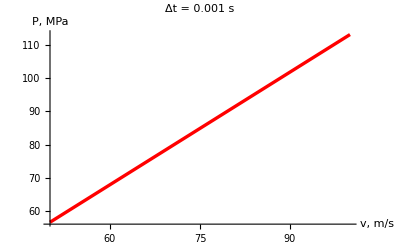

```mathematica
rys1=Plot[P×10^-6/.Δt->0.001,{v,50,100},TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     Δt = 0.001 s    ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v, m/s","P,  MPa"}]
```

### Sporzadzenie wykresu obrazujacego zaleznosc cisnienia wywieranego przez ziarna piasku na powierzchnie metalu od predkosci ziaren dla czasu zderzenia wynoszacego 0.01 s.

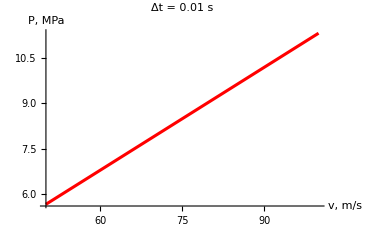

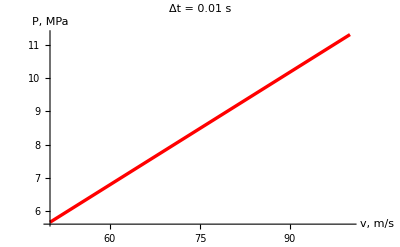

```mathematica
rys2=Plot[P×10^-6/.Δt->0.01,{v,50,100},TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     Δt = 0.01 s    ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v, m/s","P,  MPa"}]
```